```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata\\NStar"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata\NStar

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

```mathematica
Print["Runs in the list: ",runNum={12666}];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[1]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
Print["#Runs in the list: ",runn=maxCy];
Print["Storage time in the list: ",ts2=Table[15+((k-1)2.5),{k,1,maxCy}]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat1=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
runi=1;
For[icycle=1,icycle≤maxCy,icycle++,
Clear[data,histdata2];
bkgcou[[runi]]={};
moncou[[runi]]={};
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]],"  ,  ",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat1[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat1[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat1[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat1[[runi]][[i]][[2]][[1]]];
];
];,
ProgressIndicator[icycle/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
(***)
Clear[nlm,aa]
stft=160;
endft=55;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
(*Print["Cycle # 1",runNum[[runi]],"  ,  ",icycle,"  ,  ",ts2[[icycle]]];*)
ftdat=Table[Transpose[{ptdat1[[icycle]][[;;,1]],ptdat1[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat1[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["t_filling = ",ToString[Round[ts2[[icycle]]]]," s, N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=3;
exppt1=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft1=Select[ptft,#[[2]][[2]]<1&];
(************************************************)
Print["Runs in the list: ",runNum={12668}];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[1]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
Print["#Runs in the list: ",runn=maxCy];
Print["Storage time in the list: ",ts2=Table[22.5+((k-1)2.5),{k,1,maxCy}]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
runi=1;
For[icycle=1,icycle≤maxCy,icycle++,
Clear[data,histdata2];
bkgcou[[runi]]={};
moncou[[runi]]={};
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]],"  ,  ",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat2[[runi]][[i]][[2]][[1]]];
];
];,
ProgressIndicator[icycle/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
(***)
Clear[nlm,aa]
stft=70;
endft=55;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
(*Print["Cycle # 2",runNum[[runi]],"  ,  ",icycle,"  ,  ",ts2[[icycle]]];*)
If[icycle==5,endft=35];
ftdat=Table[Transpose[{ptdat2[[icycle]][[;;,1]],ptdat2[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["t_filling = ",ToString[Round[ts2[[icycle]]]]," s, N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]]+1,2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=3;
exppt2=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft2=Select[ptft,#[[2]][[2]]<1&];
```

Runs in the list: {12666}

#Runs in the list: 9.

Storage time in the list: {15.,17.5,20.,22.5,25.,27.5,30.,32.5,35.}

Read Run #12666  ,  1

Read Run #12666  ,  2

Read Run #12666  ,  3

Read Run #12666  ,  4

Read Run #12666  ,  5

Read Run #12666  ,  6

Read Run #12666  ,  7

Read Run #12666  ,  8

Read Run #12666  ,  9

Runs in the list: {12668}

#Runs in the list: 5.

Storage time in the list: {22.5,25.,27.5,30.,32.5}

Read Run #12668  ,  1

Read Run #12668  ,  2

Read Run #12668  ,  3

Read Run #12668  ,  4

Read Run #12668  ,  5

```mathematica
Export[StringJoin[PicDir,"\\","t_emptying-filling90.png"],exppt1]
Export[StringJoin[PicDir,"\\","t_emptying-filling180.png"],exppt2]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\t_emptying-filling90.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\t_emptying-filling180.png

11.0122

0.39849

11.122

0.689833

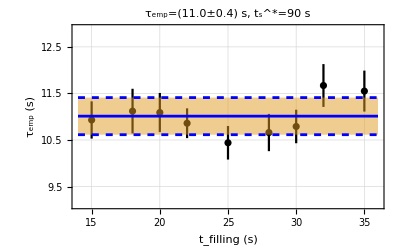

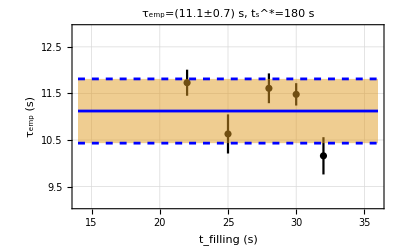

```mathematica
mean1=Mean[ptft1[[;;,2]][[;;,1]]]
sd1=StandardDeviation[ptft1[[;;,2]][[;;,1]]]
mean2=Mean[ptft2[[;;,2]][[;;,1]]]
sd2=StandardDeviation[ptft2[[;;,2]][[;;,1]]]
Show[{
EDAListPlot[ptft1,PlotRange->{{14,36},{9.1,12.9}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_filling (s)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(11.0±0.4) s, t_s^*=90 s"],
Plot[{mean1,mean1-sd1,mean1+sd1,mean1-sd1,mean1+sd1},{x,14,36},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None,{Blue,Thickness[.005],Dashed},{Blue,Thickness[.005],Dashed}}]
}]
Show[{
EDAListPlot[ptft2,PlotRange->{{14,36},{9.1,12.9}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_filling (s)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(11.1±0.7) s, t_s^*=180 s"],
Plot[{mean2,mean2-sd2,mean2+sd2,mean2-sd2,mean2+sd2},{x,14,36},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None,{Blue,Thickness[.005],Dashed},{Blue,Thickness[.005],Dashed}}]
}]
```

## τ-Monitor

```mathematica
Print["Runs in the list: ",runNum={12436}];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[1]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
Print["#Runs in the list: ",runn=maxCy];
Print["Storage time in the list: ",ts2=-{333,327,322,317,314,311,308,300}];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat3=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
runi=1;
For[icycle=1,icycle≤maxCy,icycle++,
Clear[data,histdata2];
bkgcou[[runi]]={};
moncou[[runi]]={};
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]],"  ,  ",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat3[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat3[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat3[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat3[[runi]][[i]][[2]][[1]]];
];
];,
ProgressIndicator[icycle/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
(***)
```

Runs in the list: {12436}

#Runs in the list: 8.

Storage time in the list: {-333,-327,-322,-317,-314,-311,-308,-300}

Read Run #12436  ,  1

Read Run #12436  ,  2

Read Run #12436  ,  3

Read Run #12436  ,  4

Read Run #12436  ,  5

Read Run #12436  ,  6

Read Run #12436  ,  7

Read Run #12436  ,  8

```mathematica
Clear[nlm,aa]
stft=10;
endft=35;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
(*Print["Cycle # 1",runNum[[runi]],"  ,  ",icycle,"  ,  ",ts2[[icycle]]];*)
ftdat=Table[Transpose[{ptdat3[[icycle]][[;;,1]],ptdat3[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[stft],Round[stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat3[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["Switch_(pos.) = ",ToString[Round[23+ts2[[icycle]]]]," , N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[stft],Round[stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=3;
exppt3=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft3=Select[ptft,#[[2]][[2]]<1&];
```

5.30488

0.0789927

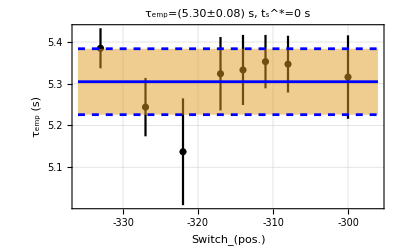

```mathematica
mean3=Mean[ptft3[[;;,2]][[;;,1]]]
sd3=StandardDeviation[ptft3[[;;,2]][[;;,1]]]
Show[{
EDAListPlot[ptft3,PlotRange->{{-296,-336},{4.91,5.49}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"Switch_(pos.)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(5.30±0.08) s, t_s^*=0 s"],
Plot[{mean3,mean3-sd3,mean3+sd3,mean3-sd3,mean3+sd3},{x,-296,-336},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None,{Blue,Thickness[.005],Dashed},{Blue,Thickness[.005],Dashed}}]
}]
```

```mathematica
Export[StringJoin[PicDir,"\\","t_emptying-monitor.png"],exppt3]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\t_emptying-monitor.png

## τ-Monitor

```mathematica
Print["Runs in the list: ",runNum={12436}];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[1]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
Print["#Runs in the list: ",runn=maxCy];
Print["Storage time in the list: ",ts2=-{333,327,322,317,314,311,308,300}];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat3=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
runi=1;
For[icycle=1,icycle≤maxCy,icycle++,
Clear[data,histdata2];
bkgcou[[runi]]={};
moncou[[runi]]={};
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]],"  ,  ",icycle];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat3[[icycle]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat3[[icycle]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat3[[icycle]][[i]][[2]][[2]]=Sqrt[ptdat3[[runi]][[i]][[2]][[1]]];
];
];,
ProgressIndicator[icycle/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
(***)
```

Runs in the list: {12436}

#Runs in the list: 8.

Storage time in the list: {-333,-327,-322,-317,-314,-311,-308,-300}

Read Run #12436  ,  1

Read Run #12436  ,  2

Read Run #12436  ,  3

Read Run #12436  ,  4

Read Run #12436  ,  5

Read Run #12436  ,  6

Read Run #12436  ,  7

Read Run #12436  ,  8

```mathematica
Clear[nlm,aa]
stft=10;
endft=35;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
(*Print["Cycle # 1",runNum[[runi]],"  ,  ",icycle,"  ,  ",ts2[[icycle]]];*)
ftdat=Table[Transpose[{ptdat3[[icycle]][[;;,1]],ptdat3[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[stft],Round[stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat3[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["Switch_(pos.) = ",ToString[Round[23+ts2[[icycle]]]]," , N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[stft],Round[stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=3;
exppt3=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft3=Select[ptft,#[[2]][[2]]<1&];
```

```mathematica
mean3=Mean[ptft3[[;;,2]][[;;,1]]]
sd3=StandardDeviation[ptft3[[;;,2]][[;;,1]]]
Show[{
EDAListPlot[ptft3,PlotRange->{{-296,-336},{4.91,5.49}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"Switch_(pos.)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotLabel-> "τ_emp=(5.30±0.08) s, t_s^*=0 s"],
Plot[{mean3,mean3-sd3,mean3+sd3,mean3-sd3,mean3+sd3},{x,-296,-336},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None,{Blue,Thickness[.005],Dashed},{Blue,Thickness[.005],Dashed}}]
}]
```

5.30488

0.0789927

-Graphics-

```mathematica
Export[StringJoin[PicDir,"\\","t_emptying-monitor.png"],exppt3]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\t_emptying-monitor.png

```mathematica
N[1/17]
N[1/41]
```

0.0588235

0.0243902

## τ-West1

```mathematica
dat=ReadList[StringJoin[AscDir,"\\","T311017_0006.stof"],{Real}];
ptdat4=Table[{},{k,1,1}];
ftdat=Table[{.1k,dat[[k]][[1]]},{k,1,Dimensions[dat][[1]]}];
ptdat4[[1]]=Table[{.1k,{dat[[k]][[1]],Sqrt[dat[[k]]][[1]]}},{k,1,Dimensions[dat][[1]]}];
runn=1;
Clear[nlm,aa]
stft=10;
endft=250;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
(*Print["Cycle # 1",runNum[[runi]],"  ,  ",icycle,"  ,  ",ts2[[icycle]]];*)
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[(xx-dd)/cc])+(ee Exp[(xx-dd)/ff]),{aa>0,bb>1,ee>1}},{{aa,1},{bb,30000},{cc,-17},{dd,33},{ee,10000},{ff,-41}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]],ee/.nlm[[1]][[2]],ff/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat4[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,350},{1,1000000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin[ToString[fitparam[[2]]],"Exp[(t-t_0)/",ToString[fitparam[[3]]],"] + \n",ToString[fitparam[[5]]],"Exp[(t-t_0)/",ToString[fitparam[[6]]],"]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[(k-fitparam[[4]])/fitparam[[3]]]+fitparam[[5]]Exp[(k-fitparam[[4]])/fitparam[[6]]]]},{k,Round[stft],Round[stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,350},{.1,400000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=1;
exppt4=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
ptft4=Select[ptft,#[[2]][[2]]<1&];
Show[{
EDALogListPlot[ptdat4[[1]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,350},{1,1000000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotMarkers->{Automatic, Medium},
PlotLabel->"N_1Exp[-(t-t_0)/(17.87±0.09)]+N_2Exp[-(t-t_0)/(41.10±0.10)]"],
EDALogListPlot[Table[{k,(6*10^4)Exp[-k/17]+(9*10^4)Exp[-k/41]},{k,Round[stft],Round[stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,350},{.1,400000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotMarkers->{Automatic, None}]
}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

-Graphics-

## FillingCurve/τ-west1

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata\NStar

Runs in the list: {12666,12667,12668,12669}

Size: 4

FittedModel[0.000182875-0.000938834 (1.53261-t)]

FittedModel[105.314-108.255 ⅇ^(-0.00243316 t)]

Number of Cycles: 9.

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.000182875 | 0.000833055 | 0.219523 | 0.834923
bb | -0.149553 | 0.00545228 | -27.4295 | 1.20518×10^-6
cc | -159.297 | 5.11879×10^-6 | -3.112×10^7 | 6.50288×10^-37
dd | 1.53261 | 7.821×10^-7 | 1.95961×10^6 | 6.56829×10^-31

| Estimate | Standard Error | t-Statistic | P-Value
aa | 105.314 | 1169.11 | 0.0900804 | 0.936432
bb | 108.255 | 1166.42 | 0.0928093 | 0.934515
cc | 410.988 | 4745.54 | 0.086605 | 0.938876

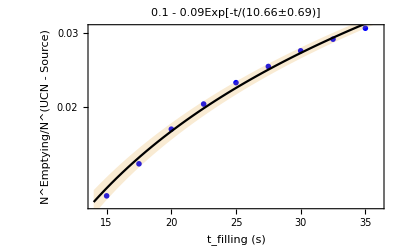

```mathematica
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata\\NStar"];
];
Print["Runs in the list: ",runNum={12666,12667,12668,12669}];(*11159,11369*)
Print["Size: ",Dimensions[runNum][[1]]];
metadata=Table[{},{k,0,Dimensions[runNum][[1]]}];
For[i=1,i≤Dimensions[runNum][[1]],i++,
metadata[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[i]],10,6],"_Meta3.edm"],metaStructure2];
];
dat=Table[{15+((k-1)2.5),{.01(metadata[[1]][[k]][[27]]+metadata[[1]][[k]][[28]]+metadata[[2]][[k]][[27]]+metadata[[2]][[k]][[28]])/(((6)Exp[-(15+((k-1)2.5))/17]+(9)Exp[-(15+((k-1)2.5))/41])*2000),Sqrt[(metadata[[1]][[k]][[27]]+metadata[[1]][[k]][[28]]+metadata[[2]][[k]][[27]]+metadata[[2]][[k]][[28]])/2]/1000}},{k,1,9}];
dat2=Table[{22.5+((k-1)2.5),{(metadata[[3]][[k]][[27]]+metadata[[3]][[k]][[28]]+metadata[[4]][[k]][[27]]+metadata[[4]][[k]][[28]])/(((6*10^4)Exp[-(22.5+((k-1)2.5))/17]+(9)Exp[-(22.5+((k-1)2.5))/41])),Sqrt[(metadata[[3]][[k]][[27]]+metadata[[3]][[k]][[28]]+metadata[[4]][[k]][[27]]+metadata[[4]][[k]][[28]])/2]/1000}},{k,1,5}];
fitt=Fit[Transpose[{dat[[;;,1]],dat[[;;,2]][[;;,1]]}],{1,t},t];
fit1=NonlinearModelFit[Transpose[{dat[[;;,1]],dat[[;;,2]][[;;,1]]}],(aa-bb (-(t-dd)/cc)),{{aa,1},{bb,1},{cc,10},{dd,1}},t,Method->NMinimize]
fit2=NonlinearModelFit[Transpose[{dat2[[;;,1]],dat2[[;;,2]][[;;,1]]}],(aa-bb Exp[-t/cc]),{aa,bb,cc},t,Method->NMinimize]
Print["Number of Cycles: ",maxCy=metadata[[1]][[-1]][[2]]];
fit1["ParameterTable"]
fit2["ParameterTable"]
Show[{EDALogListPlot[dat,PlotStyle->{{Blue,Thickness[.005]},{Red,Dashed,Thickness[.005]}},PlotRange->{{14,36},Automatic},Frame->True,FrameLabel->{"t_filling (s)","N^Emptying/N^(UCN - Source)"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black,Bold},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Large},PlotLabel->"0.1 - 0.09Exp[-t/(10.66±0.69)]"],
LogPlot[{fitt,fitt+.0008,fitt-.0008},{t,14,36},Filling->{2->{3}},PlotStyle->{{Black,Thickness[.004]},None,None}]
}]
```